# AssociationOuter

Compute the generalized outer product of lists and get an association keyed by arguments

## Definition

```mathematica
AssociationOuter // ClearAll;
```

### Initialization

```mathematica
$inDef = False;
$debug = True;
```

#### beginDefinition

```mathematica
beginDefinition // ClearAll;
```

```mathematica
beginDefinition // Attributes = { HoldFirst };
```

```mathematica
beginDefinition::unfinished = "\
Starting definition for `1` without ending the current one.";
```

:!CodeAnalysis::BeginBlock::

:!CodeAnalysis::Disable::SuspiciousSessionSymbol::

```mathematica
beginDefinition[ s_Symbol ] /; $debug && $inDef :=
    WithCleanup[
        $inDef = False
        ,
        Print @ TemplateApply[ beginDefinition::unfinished, HoldForm @ s ];
        beginDefinition @ s
        ,
        $inDef = True
    ];
```

:!CodeAnalysis::EndBlock::

```mathematica
beginDefinition[ s_Symbol ] :=
    WithCleanup[ Unprotect @ s; ClearAll @ s, $inDef = True ];
```

#### endDefinition

```mathematica
endDefinition // beginDefinition;
```

```mathematica
endDefinition // Attributes = { HoldFirst };
```

```mathematica
endDefinition[ s_Symbol ] := endDefinition[ s, DownValues ];
```

```mathematica
endDefinition[ s_Symbol, None ] := $inDef = False;
```

```mathematica
endDefinition[ s_Symbol, DownValues ] :=
    WithCleanup[
        AppendTo[ DownValues @ s,
                  e: HoldPattern @ s[ ___ ] :>
                      throwInternalFailure @ HoldForm @ e
        ],
        $inDef = False
    ];
```

```mathematica
endDefinition[ s_Symbol, SubValues  ] :=
    WithCleanup[
        AppendTo[ SubValues @ s,
                  e: HoldPattern @ s[ ___ ][ ___ ] :>
                      throwInternalFailure @ HoldForm @ e
        ],
        $inDef = False
    ];
```

```mathematica
endDefinition[ s_Symbol, list_List ] :=
    endDefinition[ s, # ] & /@ list;
```

```mathematica
endDefinition // endDefinition;
```

### Messages

```mathematica
AssociationOuter::internal =
"An unexpected error occurred. `1`";
```

```mathematica
AssociationOuter::rffail =
"Failed to retrieve definitions for the required resource function `1`.";
```

```mathematica
AssociationOuter::list =
"List expected at position `1` in `2`.";
```

### Attributes

```mathematica
AssociationOuter // Attributes = { };
```

### Options

```mathematica
AssociationOuter // Options = { };
```

### Argument patterns

```mathematica
$list  = _List | _SparseArray? SparseArrayQ;
$level = _Integer? Positive | Infinity;
$arg   = $list | $level;
```

### Main definition

```mathematica
AssociationOuter[ f_, lists: $list.., level: $level... ] :=
    catchTop @ Module[ { rules, assoc },
        rules = makeRules[ f, lists, level ];
        assoc = makeAssoc @ rules;
        AssociationKeyDeflatten @ assoc
    ];
```

### Error cases

Invalid argument count:

```mathematica
AssociationOuter[ ] :=
    catchTop @ throwFailure[ "argm", AssociationOuter, 0, 2 ];
```

AssociationOuter cannot replicate the one-argument behavior of Outer:

```mathematica
AssociationOuter[ f_ ] :=
    catchTop @ throwFailure[ "argm", AssociationOuter, 1, 2 ];
```

Invalid level spec:

```mathematica
AssociationOuter[ f_, a: $list.., b: $level..., c: Except[ $arg ], d___ ] :=
    catchTop @ throwFailure[
        "ipnfm",
        HoldForm @ AssociationOuter[ f, a, b, c, d ],
        Length @ HoldComplete[ f, a, b, c ]
    ];
```

Invalid list arguments:

```mathematica
AssociationOuter[ f_, a: $list..., b: Except[ $arg ], c___ ] :=
    catchTop @ With[ { tag = If[ AtomQ @ Unevaluated @ b, "normal", "list" ] },
        throwFailure[
            tag,
            Length @ HoldComplete[ f, a, b ],
            HoldForm @ AssociationOuter[ f, a, b, c ]
        ]
    ];
```

Missed something that needs to be fixed:

```mathematica
e: AssociationOuter[ ___ ] :=
    catchTop @ throwInternalFailure @ e;
```

### Dependencies

#### Misc utilities

##### makeRules

```mathematica
makeRules // beginDefinition;
```

```mathematica
makeRules // Attributes = { HoldAllComplete };
```

```mathematica
makeRules[ f_, a___ ] :=
    Replace[ Unevaluated /@ HoldComplete @ a,
             HoldComplete[ e___ ] :> checkOuter @ Outer[ makeOuterFunc @ f, e ]
    ];
```

```mathematica
makeRules // endDefinition;
```

##### checkOuter

```mathematica
checkOuter // beginDefinition;
checkOuter[ list_List ] := Flatten @ list;
checkOuter // endDefinition;
```

##### makeOuterFunc

```mathematica
makeOuterFunc // beginDefinition;
makeOuterFunc // Attributes = { HoldAllComplete };
makeOuterFunc[ f_ ] := Function[ Null, keys @ ## -> f @ ##, HoldAllComplete ];
makeOuterFunc // endDefinition;
```

##### makeAssoc

```mathematica
makeAssoc // beginDefinition;
```

```mathematica
makeAssoc[ { a___ } ] :=
    UnevaluatedAssociation @@ (HoldComplete @ a /. keys -> List);
```

```mathematica
makeAssoc // endDefinition;
```

##### keys

```mathematica
keys // ClearAll;
keys // Attributes = { HoldAllComplete };
```

#### Error handling

##### catchTop

```mathematica
catchTop // beginDefinition;
```

```mathematica
catchTop // Attributes = { HoldFirst };
```

```mathematica
catchTop[ eval_ ] :=
    Block[ { $catching = True, $failed = False, catchTop = # & },
        Catch[ eval, $top ]
    ];
```

```mathematica
catchTop // endDefinition;
```

##### throwFailure

```mathematica
throwFailure // beginDefinition;
```

```mathematica
throwFailure // Attributes = { HoldFirst };
```

```mathematica
throwFailure[ tag_String, params___ ] :=
    throwFailure[ MessageName[ AssociationOuter, tag ], params ];
```

```mathematica
throwFailure[ msg_, args___ ] :=
    Module[ { failure },
        failure = messageFailure[ msg, Sequence @@ HoldForm /@ { args } ];
        If[ TrueQ @ $catching,
            Throw[ failure, $top ],
            failure
        ]
    ];
```

```mathematica
throwFailure // endDefinition;
```

##### messageFailure

```mathematica
messageFailure // beginDefinition;
```

```mathematica
messageFailure // Attributes = { HoldFirst };
```

```mathematica
messageFailure[ args___ ] :=
    Module[ { quiet },
        quiet = If[ TrueQ @ $failed, Quiet, Identity ];
        WithCleanup[ quiet @ MessageFailure @ args, $failed = True ]
    ];
```

```mathematica
messageFailure // endDefinition;
```

##### throwInternalFailure

```mathematica
throwInternalFailure // beginDefinition;
```

```mathematica
throwInternalFailure // Attributes = { HoldFirst };
```

```mathematica
throwInternalFailure[ eval_, a___ ] :=
    throwFailure[
        AssociationOuter::internal,
        $bugReportLink,
        HoldForm @ eval,
        a
    ];
```

```mathematica
throwInternalFailure // endDefinition;
```

##### $bugReportLink

```mathematica
$bugReportLink := $bugReportLink = Hyperlink[
    "Report this issue »",
    URLBuild @ <|
        "Scheme"   -> "https",
        "Domain"   -> "resources.wolframcloud.com",
        "Path"     -> { "FunctionRepository", "feedback-form" },
        "Fragment" -> SymbolName @ AssociationOuter
    |>
];
```

### External Dependencies

#### Utilities

##### $selfResourceFunction

```mathematica
$selfResourceFunction // ClearAll;
```

```mathematica
$selfResourceFunction /: Set[ s_, $selfResourceFunction ] :=
    With[ { n = SymbolName @ Unevaluated @ s },
        s // ClearAll;
        s := Enclose[
            s = Block[ { PrintTemporary },
                    Confirm @ ResourceFunction[ n, "Function" ]
                ],
            throwFailure[ "rffail", n ] &
        ];
    ];
```

#### ResourceFunctions

```mathematica
AssociationKeyDeflatten = $selfResourceFunction;
UnevaluatedAssociation  = $selfResourceFunction;
MessageFailure          = $selfResourceFunction;
```

## Documentation

### Usage

AssociationOuter[f,list_1,list_2,…]

gives the generalized outer product of the list_i as a nested association, forming all possible combinations of the lowest-level elements in each of them as keys, and feeding them as arguments to f for values.

AssociationOuter[f,list_1,list_2,…,n]

treats as separate elements only sublists at level n in the list_i.

AssociationOuter[f,list_1,list_2,…,n_1,n_2,…]

treats as separate elements only sublists at level n_i in the corresponding list_i.

### Details & Options

AssociationOuter[f,list_1,list_2,…] computes all the same f[…] as Outer[f,list_1,list_2,…]

AssociationOuter[Times,list_1,list_2] gives an outer product.

Unlike Outer, the heads of all list_i must be List.

The list_i need not necessarily be cuboidal arrays.

The specifications n_i of levels must be positive integers, or Infinity.

If only a single level specification is given, it is assumed to apply to all the list_i. If there are several n_i, but fewer than the number of list_i, the lowest-level elements in the remaining list_i will be used.

AssociationOuter can be used on SparseArray objects, returning a SparseArray object when possible.

AssociationOuter[f,list] is effectively equivalent to AssociationMap[f,list].

## Examples

### Basic Examples

Compute an outer product:

```mathematica
AssociationOuter[f,{a,b},{x,y,z}]
```

<|a→<|x→f[a,x],y→f[a,y],z→f[a,z]|>,b→<|x→f[b,x],y→f[b,y],z→f[b,z]|>|>

Compare to Outer:

```mathematica
Outer[f,{a,b},{x,y,z}]
```

{{f[a,x],f[a,y],f[a,z]},{f[b,x],f[b,y],f[b,z]}}

Outer product of vectors:

```mathematica
AssociationOuter[Times,{1,2,3,4},{a,b,c}]
```

<|1→<|a→a,b→b,c→c|>,2→<|a→2 a,b→2 b,c→2 c|>,3→<|a→3 a,b→3 b,c→3 c|>,4→<|a→4 a,b→4 b,c→4 c|>|>

Outer product of matrices:

```mathematica
AssociationOuter[Times,{{1,2},{3,4}},{{a,b},{c,d}}]
```

<|1→<|a→a,b→b,c→c,d→d|>,2→<|a→2 a,b→2 b,c→2 c,d→2 d|>,3→<|a→3 a,b→3 b,c→3 c,d→3 d|>,4→<|a→4 a,b→4 b,c→4 c,d→4 d|>|>

### Scope

The keys are nested so that values can be retrieved in argument order:

```mathematica
as=AssociationOuter[f,{a,b},{x,y,z},{u,v}]
```

<|a→<|x→<|u→f[a,x,u],v→f[a,x,v]|>,y→<|u→f[a,y,u],v→f[a,y,v]|>,z→<|u→f[a,z,u],v→f[a,z,v]|>|>,b→<|x→<|u→f[b,x,u],v→f[b,x,v]|>,y→<|u→f[b,y,u],v→f[b,y,v]|>,z→<|u→f[b,z,u],v→f[b,z,v]|>|>|>

```mathematica
as[a,y,u]
```

f[a,y,u]

```mathematica
as[b,x,v]
```

f[b,x,v]

Treat nested lists as rank-1 vectors of sublists:

```mathematica
AssociationOuter[f,{{1,2},{3,4}},{{a,b},{c,d}},1]
```

<|{1,2}→<|{a,b}→f[{1,2},{a,b}],{c,d}→f[{1,2},{c,d}]|>,{3,4}→<|{a,b}→f[{3,4},{a,b}],{c,d}→f[{3,4},{c,d}]|>|>

Arrays can be ragged:

```mathematica
AssociationOuter[Times,{{1,2},{3,4}},{{a,b,c},{d,e}}]
```

<|1→<|a→a,b→b,c→c,d→d,e→e|>,2→<|a→2 a,b→2 b,c→2 c,d→2 d,e→2 e|>,3→<|a→3 a,b→3 b,c→3 c,d→3 d,e→3 e|>,4→<|a→4 a,b→4 b,c→4 c,d→4 d,e→4 e|>|>

Outer product of SparseArraypaclet:ref/SparseArray objects:

```mathematica
s1=SparseArray[Table[2^i->i,{i,3}]];
s2=SparseArray[{1}->1,{4}];
```

```mathematica
AssociationOuter[Times,s1,s2]
```

<|0→<|1→0,0→0|>,1→<|1→1,0→0|>,2→<|1→2,0→0|>,3→<|1→3,0→0|>|>

### Applications

Word combinations:

```mathematica
AssociationOuter[StringJoin,{"","re","un"},{"cover","draw","wind"},{"","ing","s"}]
```

<|→<|cover→<|→cover,ing→covering,s→covers|>,draw→<|→draw,ing→drawing,s→draws|>,wind→<|→wind,ing→winding,s→winds|>|>,re→<|cover→<|→recover,ing→recovering,s→recovers|>,draw→<|→redraw,ing→redrawing,s→redraws|>,wind→<|→rewind,ing→rewinding,s→rewinds|>|>,un→<|cover→<|→uncover,ing→uncovering,s→uncovers|>,draw→<|→undraw,ing→undrawing,s→undraws|>,wind→<|→unwind,ing→unwinding,s→unwinds|>|>|>

Function combinations:

```mathematica
fm=AssociationOuter[Composition,{Sin,Cos,Exp},{ArcSin,ArcCos,Log}]
```

<|Sin→<|ArcSin→Sin@*ArcSin,ArcCos→Sin@*ArcCos,Log→Sin@*Log|>,Cos→<|ArcSin→Cos@*ArcSin,ArcCos→Cos@*ArcCos,Log→Cos@*Log|>,Exp→<|ArcSin→Exp@*ArcSin,ArcCos→Exp@*ArcCos,Log→Exp@*Log|>|>

```mathematica
GraphicsGrid@Map[Function[f,Plot3D[Re[f[x+I y]],{x,-2,2},{y,-2,2},Mesh->None]],Map[Values,fm,{0,1}],{2}]
```

-Graphics-

Complete bipartite graph:

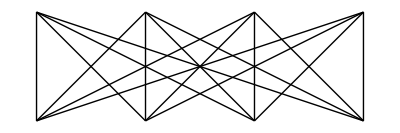

```mathematica
Graphics[Values[[AssociationOuter[Line[ {##}]&,Table[{x,1},{x,4}],Table[{x,2},{x,4}],1]]]]
```

Generate all possible binary trees with nodes from f and leaves from e to depth n:

```mathematica
trees[f_,e_,1]=e;
trees[f_,e_,n_]:=Flatten[Table[AssociationOuter[#,trees[f,e,r],trees[f,e,n-r]],{r,n-1}]&/@f]
```

```mathematica
trees[{f},{a,b},3]
```

{<|a→<|<|a→<|a→f[a,a],b→f[a,b]|>,b→<|a→f[b,a],b→f[b,b]|>|>→f[a,<|a→<|a→f[a,a],b→f[a,b]|>,b→<|a→f[b,a],b→f[b,b]|>|>]|>,b→<|<|a→<|a→f[a,a],b→f[a,b]|>,b→<|a→f[b,a],b→f[b,b]|>|>→f[b,<|a→<|a→f[a,a],b→f[a,b]|>,b→<|a→f[b,a],b→f[b,b]|>|>]|>|>,<|<|a→<|a→f[a,a],b→f[a,b]|>,b→<|a→f[b,a],b→f[b,b]|>|>→<|a→f[<|a→<|a→f[a,a],b→f[a,b]|>,b→<|a→f[b,a],b→f[b,b]|>|>,a],b→f[<|a→<|a→f[a,a],b→f[a,b]|>,b→<|a→f[b,a],b→f[b,b]|>|>,b]|>|>}

### Properties & Relations

If each of the list_i are duplicate-free, dimensions of the result are a concatenation of the dimensions of the inputs:

```mathematica
AssociationOuter[f,{a,b,c},{1,2,3,4}]
```

<|a→<|1→f[a,1],2→f[a,2],3→f[a,3],4→f[a,4]|>,b→<|1→f[b,1],2→f[b,2],3→f[b,3],4→f[b,4]|>,c→<|1→f[c,1],2→f[c,2],3→f[c,3],4→f[c,4]|>|>

```mathematica
Dimensions[%]
```

{3,4}

If there are duplicates, the dimensions will correspond to the number of unique elements in each list_i:

```mathematica
AssociationOuter[f,{a,a,a},{1,2,2,3}]
```

<|a→<|1→f[a,1],2→f[a,2],3→f[a,3]|>|>

```mathematica
Dimensions[%]
```

{1,3}

Compare to Outer, which is unaffected by duplicates:

```mathematica
Outer[f,{a,a,a},{1,2,2,3}]
```

{{f[a,1],f[a,2],f[a,2],f[a,3]},{f[a,1],f[a,2],f[a,2],f[a,3]},{f[a,1],f[a,2],f[a,2],f[a,3]}}

```mathematica
Dimensions[%]
```

{3,4}

Use Map and Values to convert the result into the format given by Outer:

```mathematica
AssociationOuter[f,{a,b},{x,y,z}]
```

<|a→<|x→f[a,x],y→f[a,y],z→f[a,z]|>,b→<|x→f[b,x],y→f[b,y],z→f[b,z]|>|>

```mathematica
Map[Values,%,{0,1}]
```

{{f[a,x],f[a,y],f[a,z]},{f[b,x],f[b,y],f[b,z]}}

```mathematica
Outer[f,{a,b},{x,y,z}]
```

{{f[a,x],f[a,y],f[a,z]},{f[b,x],f[b,y],f[b,z]}}

AssociationKeyFlatten can be used to convert the result into a flat association:

```mathematica
as=AssociationOuter[f,{a,b},{x,y,z}]
```

<|a→<|x→f[a,x],y→f[a,y],z→f[a,z]|>,b→<|x→f[b,x],y→f[b,y],z→f[b,z]|>|>

```mathematica
flat={{"[◼]", "AssociationKeyFlatten"}}[as]
```

<|{a,x}→f[a,x],{a,y}→f[a,y],{a,z}→f[a,z],{b,x}→f[b,x],{b,y}→f[b,y],{b,z}→f[b,z]|>

Restore the nested structure with AssociationKeyDeflatten:

```mathematica
{{"[◼]", "AssociationKeyDeflatten"}}[flat]
```

<|a→<|x→f[a,x],y→f[a,y],z→f[a,z]|>,b→<|x→f[b,x],y→f[b,y],z→f[b,z]|>|>

Distribute forms the same combinations of all elements, but in a flat structure:

```mathematica
Distribute[{{a,b,c},{x,y}},List]
```

{{a,x},{a,y},{b,x},{b,y},{c,x},{c,y}}

```mathematica
AssociationOuter[List,{a,b,c},{x,y}]
```

<|a→<|x→{a,x},y→{a,y}|>,b→<|x→{b,x},y→{b,y}|>,c→<|x→{c,x},y→{c,y}|>|>

Use AssociationKeyFlatten and Values to get the same result:

```mathematica
Values[{{"[◼]", "AssociationKeyFlatten"}}[%]]
```

{{a,x},{a,y},{b,x},{b,y},{c,x},{c,y}}

AssociationOuter relates to Outer much like AssociationMap relates to Map:

```mathematica
AssociationOuter[f,{1,2,3}]
```

<|1→f[1],2→f[2],3→f[3]|>

```mathematica
Outer[f,{1,2,3}]
```

{f[1],f[2],f[3]}

```mathematica
AssociationMap[f,{1,2,3}]
```

<|1→f[1],2→f[2],3→f[3]|>

```mathematica
Map[f,{1,2,3}]
```

{f[1],f[2],f[3]}

### Possible Issues

Unlike Outer, the head must be List:

```mathematica
AssociationOuter[g,f[a,b],f[x,y,z]]
```

AssociationOuter::list: List expected at position 2 in AssociationOuter[g,f[a,b],f[x,y,z]].

Failure[…]

```mathematica
Outer[g,f[a,b],f[x,y,z]]
```

f[f[g[a,x],g[a,y],g[a,z]],f[g[b,x],g[b,y],g[b,z]]]

Unlike Outer, at least two arguments are required:

```mathematica
AssociationOuter[f]
```

AssociationOuter::argm: AssociationOuter called with 1 arguments; 2 or more arguments are expected.

Failure[…]

```mathematica
Outer[f]
```

f[]

Values are nested by arguments in the order they were given to f, even if f is Orderless:

```mathematica
as=AssociationOuter[Plus,{1,2,3},{4,5}]
```

<|1→<|4→5,5→6|>,2→<|4→6,5→7|>,3→<|4→7,5→8|>|>

```mathematica
as[4,1]
```

Missing[KeyAbsent,4]

```mathematica
as[1,4]
```

5

## Source & Additional Information

### Contributed By

Richard Hennigan (Wolfram Research)

### Keywords

Cartesian products

direct products

direct products tensors

dyadic products

exterior products

Kronecker products tensors

levels

matrices

outer products

tensor products

tensors

wedge product

### Categories

3D Visualization |  Accessibility
 Accessing External Services & APIs |  Associations
 Astronomical Computation & Data |  Background & Scheduled Tasks
 Calculus |  Calling External Programs
 Cloud & Deployment |  Cloud Functions & Deployment
 Code as Data |  Color Processing
 Computational Geometry |  Computation on Graphs
 Computer Vision |  Control Objects
 Core Language & Structure |  Creating Form Interfaces & Apps
 Cryptography |  Cultural Data
 Data Manipulation & Analysis |  Data Structures
 Data Transforms and Smoothing |  Data Visualization
 Date & Time |  Decorations
 Differential Geometry |  Dimension Reduction
 Discrete Mathematics |  Dynamic Interactivity Language
 Engineering Data & Computation |  Error Handling
 Expressions |  External Interfaces & Connections
 External Language Interfaces |  File Operations
 Financial Data & Computation |  Front End Utilities
 Functional Programming |  Function Visualization
 Games |  Geographic Data and Entities
 Geographic Data & Computation |  Geographic Visualization
 Geometric Region Properties |  Geometric Transforms
 Geometry |  Graph Construction & Representation
 Graph Properties & Measurements |  Graphs & Networks
 Graph Visualization |  Handling Arrays of Data
 Higher Mathematical Computation |  Image Filtering & Neighborhood Processing
 Image Processing & Analysis |  Images
 Importing and Exporting |  Interactive Manipulation
 Iterated Maps & Fractals |  Just For Fun
 Knowledge Representation & Natural Language |  Layout & Tables
 Life Sciences & Medicine: Data & Computation |  Linguistic Data
 List Manipulation |  Logic & Boolean Algebra
 Low-Level Notebook Programming |  Machine Learning
 Maps & Cartography |  Mathematical Functions
 Matrices and Linear Algebra |  Molecular Structure & Computation
 Natural Language Processing |  Neural Networks
 Notebook Basics |  Notebook Document Generation
 Notebook Documents & Presentation |  Notebook Formatting & Styling
 Number Theory |  Numeric Approximation
 Optimization |  Parallel Computing
 Persistent Storage |  Physics & Chemistry: Data and Computation
 Plane Geometry |  Polynomial Algebra
 Precollege Education |  Presentations with the Wolfram System
 Probability & Statistics |  Programming Utilities
 Random Stuff |  Real & Complex Analysis
 Recreational Math |  Repository Tools
 RepositoryTools |  Rules & Patterns
 Scientific and Medical Data & Computation |  Scientific Data Analysis
 Segmentation Analysis |  Sequence Analysis
 Shortcuts and Idioms |  Signal Processing
 Social, Cultural & Linguistic Data |  Social Data
 Solid Geometry |  Sound & Video
 Statistical Data Analysis |  String Manipulation
 Strings & Text |  Symbolic & Numeric Computation
 System Operation & Setup |  Text Analysis
 Text Manipulation |  Theorem Proving
 Time-Related Computation |  Time Series Processing
 Topology |  Tuning & Debugging
 Units & Quantities |  User Interface Construction
 Viewers and Annotation |  Visualization & Graphics
 Weather Data |  Web Operations
 Wolfram Physics Project |  Wolfram System Setup
 Working with Paclets |

### Related Symbols

Outer

Tuples

Inner

Distribute

KroneckerProduct

Cross

Dot

Norm

DistanceMatrix

### Related Resource Objects

Outer

ParallelOuter

Unthread

AssociationKeyFlatten

AssociationKeyDeflatten

UnevaluatedAssociation

### Source/Reference Citation

Source, reference or citation information

### Links

rhennigan GitHub–AssociationOuter

### Tests

#### Initialization

```mathematica
VerificationTest[
    SetOptions[ ResourceFunction[ "MessageFailure" ], "TestMode" -> True ],
    KeyValuePattern[ "TestMode" -> True ],
    SameTest -> MatchQ
]
```

#### Tests

##### Basic Examples

```mathematica
VerificationTest[
    AssociationOuter[ f, { a, b }, { x, y, z } ],
    <|
        a -> <| x -> f[ a, x ], y -> f[ a, y ], z -> f[ a, z ] |>,
        b -> <| x -> f[ b, x ], y -> f[ b, y ], z -> f[ b, z ] |>
    |>
]
```

##### Scope

```mathematica
VerificationTest[
    AssociationOuter[f, {a, b}, {x, y, z}, {u, v}],
    <|
        a -> <|
            x -> <| u -> f[ a, x, u ], v -> f[ a, x, v ] |>,
            y -> <| u -> f[ a, y, u ], v -> f[ a, y, v ] |>,
            z -> <| u -> f[ a, z, u ], v -> f[ a, z, v ] |>
        |>,
        b -> <|
            x -> <| u -> f[ b, x, u ], v -> f[ b, x, v ] |>,
            y -> <| u -> f[ b, y, u ], v -> f[ b, y, v ] |>,
            z -> <| u -> f[ b, z, u ], v -> f[ b, z, v ] |>
        |>
    |>
]
```

```mathematica
VerificationTest[
    AssociationOuter[ f, { { 1, 2 }, { 3, 4 } }, { { a, b }, { c, d } }, 1 ],
    <|
        { 1, 2 } -> <|
            { a, b } -> f[ { 1, 2 }, { a, b } ],
            { c, d } -> f[ { 1, 2 }, { c, d } ]
        |>,
        { 3, 4 } -> <|
            { a, b } -> f[ { 3, 4 }, { a, b } ],
            { c, d } -> f[ { 3, 4 }, { c, d } ]
        |>
    |>
]
```

```mathematica
VerificationTest[
    AssociationOuter[ Times, { { 1, 2 }, { 3, 4 } }, { { a, b, c }, { d, e } } ],
    <|
        1 -> <| a -> a, b -> b, c -> c, d -> d, e -> e |>,
        2 -> <| a -> 2 * a, b -> 2 * b, c -> 2 * c, d -> 2 * d, e -> 2 * e |>,
        3 -> <| a -> 3 * a, b -> 3 * b, c -> 3 * c, d -> 3 * d, e -> 3 * e |>,
        4 -> <| a -> 4 * a, b -> 4 * b, c -> 4 * c, d -> 4 * d, e -> 4 * e |>
    |>
]
```

##### Error Cases

```mathematica
VerificationTest[
    AssociationOuter[ ],
    Failure[ "AssociationOuter::argm", _ ],
    { AssociationOuter::argm },
    SameTest -> MatchQ
]
```

```mathematica
VerificationTest[
    AssociationOuter[ f ],
    Failure[ "AssociationOuter::argm", _ ],
    { AssociationOuter::argm },
    SameTest -> MatchQ
]
```

```mathematica
VerificationTest[
    AssociationOuter[ f, { a, b, c }, x ],
    Failure[ "AssociationOuter::ipnfm", _ ],
    { AssociationOuter::ipnfm },
    SameTest -> MatchQ
]
```

```mathematica
VerificationTest[
    AssociationOuter[ f, { a, b, c }, x ],
    Failure[ "AssociationOuter::ipnfm", _ ],
    { AssociationOuter::ipnfm },
    SameTest -> MatchQ
]
```

```mathematica
VerificationTest[
    AssociationOuter[ f, x ],
    Failure[ "AssociationOuter::normal", _ ],
    { AssociationOuter::normal },
    SameTest -> MatchQ
]
```

```mathematica
VerificationTest[
    AssociationOuter[ f, g[ x ] ],
    Failure[ "AssociationOuter::list", _ ],
    { AssociationOuter::list },
    SameTest -> MatchQ
]
```

#### Cleanup

```mathematica
VerificationTest[
    SetOptions[ ResourceFunction[ "MessageFailure" ], "TestMode" -> False ],
    KeyValuePattern[ "TestMode" -> False ],
    SameTest -> MatchQ
]
```

### Compatibility

#### Wolfram Language Version

12.3+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session |  ScriptScript run in batch mode |  SubkernelParallel or grid subkernel
 WebEvaluationCloud evaluation initiated by an HTTP request |  WebAPIAPI called through an HTTP request |  ScheduledScheduled task
 BatchJobRemote batch job |  |

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.